```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/poslavsky/Projects/redberry/bcbcnlo/src/trash/check_ANDREI2_Z/PV/larin/gamma+Z/renorm

```mathematica
<<cross-sectionNLOLarin.res
```

```mathematica
ex[1]=Coefficient[crosssection,AS^2] AS^2;
```

```mathematica
ex[2]=Plus@@FullSimplify[List@@Collect[ex[1]/.{pow[s,1/2]-> s^(1/2),pow[s-4 m^2,1/2]-> (s-4 m^2)^(1/2),pi-> Pi},DEN[___]]];
```

$Aborted

```mathematica
tmp = ex[1]/.{pow[s,1/2]-> s^(1/2),pow[s-4 m^2,1/2]-> (s-4 m^2)^(1/2),pi-> Pi};
```

```mathematica
tmpG = Limit[tmp,mZ->Infinity];
```

```mathematica
tmpG = tmpG/.r->MC/(MC+MB)/.m->MC+MB;
```

```mathematica
FullSimplify@Factor[$Kiselev["PV"]/tmpG]
```

(alphaS^2 (1+cos^2) e^4 fBc^4 (MB+MC)^2)/(384 AL^2 AS^2 R1^2 R2^2)

```mathematica
LoadedAmplitudes["PV"]["tree"]
```

(64 ⅈ e gStrong^2 (MB+MC)^4 (MB^3-2 MC^3) scalar0)/(3 MB^3 MC^3 s^2)

```mathematica
ex[2]
```

```mathematica
a = andreiTree["PP"];
```

```mathematica
b = andreiTree["PP"];
```

```mathematica
(a-b)//NN
```

0.0000532793 alphaS^2 (-(3.00367×10^9 fBc^4 √(-158.76+s))/s^(13/2)+(4.6659×10^7 fBc^4 √(-158.76+s))/s^(11/2)+(3.2518×10^8 fBc^4 √(-158.76+s))/((-8315.18+s) s^(11/2))-(238770. fBc^4 √(-158.76+s))/s^(9/2)-(1.56512×10^9 fBc^4 √(-158.76+s))/((-8315.18+s)^2 s^(9/2))-(4.89215×10^6 fBc^4 √(-158.76+s))/((-8315.18+s) s^(9/2))+(403.405 fBc^4 √(-158.76+s))/s^(7/2)+(2.27802×10^7 fBc^4 √(-158.76+s))/((-8315.18+s)^2 s^(7/2))+(24111.7 fBc^4 √(-158.76+s))/((-8315.18+s) s^(7/2))-(108063. fBc^4 √(-158.76+s))/((-8315.18+s)^2 s^(5/2))-(39.043 fBc^4 √(-158.76+s))/((-8315.18+s) s^(5/2))+(167.996 fBc^4 √(-158.76+s))/((-8315.18+s)^2 s^(3/2)))-0.0000532793 alphaS^2 (-(3.00367×10^9 fBc^4 √(-158.76+s))/s^(13/2)+(4.6659×10^7 fBc^4 √(-158.76+s))/s^(11/2)-(3.2518×10^8 fBc^4 √(-158.76+s))/((-8315.18+s) s^(11/2))-(238770. fBc^4 √(-158.76+s))/s^(9/2)-(1.56512×10^9 fBc^4 √(-158.76+s))/((-8315.18+s)^2 s^(9/2))+(4.89215×10^6 fBc^4 √(-158.76+s))/((-8315.18+s) s^(9/2))+(403.405 fBc^4 √(-158.76+s))/s^(7/2)+(2.27802×10^7 fBc^4 √(-158.76+s))/((-8315.18+s)^2 s^(7/2))-(24111.7 fBc^4 √(-158.76+s))/((-8315.18+s) s^(7/2))-(108063. fBc^4 √(-158.76+s))/((-8315.18+s)^2 s^(5/2))+(39.043 fBc^4 √(-158.76+s))/((-8315.18+s) s^(5/2))+(167.996 fBc^4 √(-158.76+s))/((-8315.18+s)^2 s^(3/2)))

```mathematica
andr = andreiTree["PP"];
```

```mathematica
andr1=andr/.DEN[p1+p2,MZ,1]->1/(s-MZ^2);
andr2=andr/.(x_DEN->-x)/.DEN[p1+p2,MZ,1]->1/(s-MZ^2);
andr3=andr/.(x_DEN->I x)/.DEN[p1+p2,MZ,1]->1/(s-MZ^2);
andr4=andr/.(x_DEN->-I x)/.DEN[p1+p2,MZ,1]->1/(s-MZ^2);
```

```mathematica
tmpG=andreiTree["PP"];
```

```mathematica
tmpG//Variables
```

{alphaS,CW,e,fBc,MB,MC,MZ,s,SW}

```mathematica
FullSimplify@Factor[Limit[andr1,MZ->Infinity]/CrossSectionTree["PP"]]
```

1

```mathematica
tmp=tmpG-(CrossSectionTree["zPP"]/.GammaZ->0);
```

```mathematica
tmpG/.s->(4(MC+MB)^2)
```

0

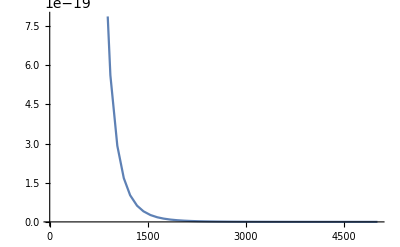

```mathematica
Block[{CW=$CW,SW=$SW,MC=$MC,MB=$MB,MZ=200,fBc=1,e=1,alphaS=0.3},
Plot[b/.s->ecm^2,{ecm,$ecmMin+10^-5,$ecmMin+5000}]
]
```

```mathematica
FullSimplify[(andr1/(CrossSectionTree["zPV"]/.GammaZ->0))/.MC->10x/.MB->13x/.MZ->99x/.SW->1/3/.CW->√(1-1/9)/.s->s x^2,s>0&&x>0]
```

(81 (-2116+s) (712344016421566739324928+s (-1574586658760797858176+s (1100144249483123821+65 s (-4009500752722+379570165 s)))))/(16 s (-62791042564490398811136+s (7922801599058365047144+s (-22029740512377490366+s (14202579237249193+1312478390925 s)))))

```mathematica
Factor[((CrossSectionTree["zVV"]/sigmaB)/.GammaZ->0)/.MC->10x/.MB->13x/.MZ->99x/.SW->1/3/.CW->√(1-1/9)/.s->s x^2]
```

(529 alphaS^2 e^4 fBc^4 (-46+√s) (46+√s) s^(13/2) (1202080527711393872610816+2827560711841094455776 s-2099500470380202357 s^2+1187327051559884 s^3+114039294525 s^4) x^14 √((-2116+s) x^2))/(128 Rs^4 (-2116+s)^(3/2) (-8562923+7995 s) (-52643261873518272+67212474212169 s-17922991421 s^2+1562340 s^3) (s x^2)^(13/2) α^2 αs^2)

```mathematica
%//NN
```

0.0424505

```mathematica
896727507659011639178777589903/14343233741438584993831434596848//N
```

0.0625192

```mathematica
sigmaB = (8 π α^2 αs^2 Rs^4 (s-4)^(3/2) ((m^2 s (4 SW^2-1) (m^2 s-M^2) (18 r^8 (s+2)^2 (2 SW^2-1)-6 r^7 (s+2) (20 s SW^2-11 s+32 SW^2-20)+r^6 (s^2 (172 SW^2-105)+s (752 SW^2-486)+832 SW^2-552)-6 r^5 (8 s^2 (3 SW^2-2)+s (152 SW^2-103)+8 (24 SW^2-17))+2 r^4 (s^2 (38 SW^2-27)+15 s (24 SW^2-17)+592 SW^2-438)+r^3 (-6 s^2 (4 SW^2-3)+s (270-368 SW^2)-896 SW^2+672)+r^2 (s^2+28 s+112) (4 SW^2-3)-4 r (s+8) (4 SW^2-3)+4 (4 SW^2-3)))/(CW^2 SW^2 (4 G^2 M^2+(M^2-m^2 s)^2))+(m^4 s^2 (8 SW^4-4 SW^2+1) (-3 r^4 (s+2)+r^3 (5 s+8)-3 r^2 (s+4)+r (s+8)-2)^2)/(CW^2 SW^2 (4 G^2 M^2+(M^2-m^2 s)^2))+8 (-3 r^4 (s+2)+r^3 (5 s+8)-3 r^2 (s+4)+r (s+8)-2)^2))/(243 m^8 (r-1)^6 r^6 s^(13/2));
```

```mathematica
sigmaB=sigmaB/.s->s/m^2/.r->MC/m/.M->MZ/.m->MC+MB/.M->MZ/.G->GammaZ;
```

```mathematica
FullSimplify[Factor[Limit[sigmaB,MZ->Infinity]]/CrossSectionTree["PP"]]
```

(144 Rs^4 α^2 αs^2)/(alphaS^2 e^4 fBc^4 (MB+MC)^2)

```mathematica
PowerExpand@√(9/((MB+MC)^2 π^2))
```

```mathematica
FullSimplify[1/√(3/((MB+MC) π))]
```

√(MB+MC) √(π/3)

```mathematica
tmpG//Variables
```

{AL,AS,cw,MB,MC,mZ,R1,R2,s,sw}

```mathematica
Factor[tmpG]
```

-((AL^2 AS^2 (MB+MC)^2 π R1^2 R2^2 (2 MB+2 MC-√s) (2 MB+2 MC+√s) √(-4 (MB+MC)^2+s) (36 MB^12 s^2+144 MB^11 MC s^2+216 MB^10 MC^2 s^2+144 MB^9 MC^3 s^2+108 MB^8 MC^4 s^2+288 MB^7 MC^5 s^2+432 MB^6 MC^6 s^2+288 MB^5 MC^7 s^2+108 MB^4 MC^8 s^2+144 MB^3 MC^9 s^2+216 MB^2 MC^10 s^2+144 MB MC^11 s^2+36 MC^12 s^2-36 MB^9 MC s^3-72 MB^8 MC^2 s^3-72 MB^7 MC^3 s^3-72 MB^6 MC^4 s^3-72 MB^5 MC^5 s^3-72 MB^4 MC^6 s^3-72 MB^3 MC^7 s^3-72 MB^2 MC^8 s^3-36 MB MC^9 s^3+9 MB^6 MC^2 s^4+18 MB^4 MC^4 s^4+9 MB^2 MC^6 s^4-192 cw^2 MB^12 mZ^2 s sw^2-768 cw^2 MB^11 MC mZ^2 s sw^2-1152 cw^2 MB^10 MC^2 mZ^2 s sw^2-768 cw^2 MB^9 MC^3 mZ^2 s sw^2-768 cw^2 MB^8 MC^4 mZ^2 s sw^2-2304 cw^2 MB^7 MC^5 mZ^2 s sw^2-3456 cw^2 MB^6 MC^6 mZ^2 s sw^2-2304 cw^2 MB^5 MC^7 mZ^2 s sw^2-960 cw^2 MB^4 MC^8 mZ^2 s sw^2-1536 cw^2 MB^3 MC^9 mZ^2 s sw^2-2304 cw^2 MB^2 MC^10 mZ^2 s sw^2-1536 cw^2 MB MC^11 mZ^2 s sw^2-384 cw^2 MC^12 mZ^2 s sw^2-240 MB^12 s^2 sw^2+192 cw^2 MB^12 s^2 sw^2-960 MB^11 MC s^2 sw^2+768 cw^2 MB^11 MC s^2 sw^2-1440 MB^10 MC^2 s^2 sw^2+1152 cw^2 MB^10 MC^2 s^2 sw^2-960 MB^9 MC^3 s^2 sw^2+768 cw^2 MB^9 MC^3 s^2 sw^2-816 MB^8 MC^4 s^2 sw^2+768 cw^2 MB^8 MC^4 s^2 sw^2-2304 MB^7 MC^5 s^2 sw^2+2304 cw^2 MB^7 MC^5 s^2 sw^2-3456 MB^6 MC^6 s^2 sw^2+3456 cw^2 MB^6 MC^6 s^2 sw^2-2304 MB^5 MC^7 s^2 sw^2+2304 cw^2 MB^5 MC^7 s^2 sw^2-912 MB^4 MC^8 s^2 sw^2+960 cw^2 MB^4 MC^8 s^2 sw^2-1344 MB^3 MC^9 s^2 sw^2+1536 cw^2 MB^3 MC^9 s^2 sw^2-2016 MB^2 MC^10 s^2 sw^2+2304 cw^2 MB^2 MC^10 s^2 sw^2-1344 MB MC^11 s^2 sw^2+1536 cw^2 MB MC^11 s^2 sw^2-336 MC^12 s^2 sw^2+384 cw^2 MC^12 s^2 sw^2+192 cw^2 MB^9 MC mZ^2 s^2 sw^2+384 cw^2 MB^8 MC^2 mZ^2 s^2 sw^2+480 cw^2 MB^7 MC^3 mZ^2 s^2 sw^2+576 cw^2 MB^6 MC^4 mZ^2 s^2 sw^2+576 cw^2 MB^5 MC^5 mZ^2 s^2 sw^2+576 cw^2 MB^4 MC^6 mZ^2 s^2 sw^2+672 cw^2 MB^3 MC^7 mZ^2 s^2 sw^2+768 cw^2 MB^2 MC^8 mZ^2 s^2 sw^2+384 cw^2 MB MC^9 mZ^2 s^2 sw^2+240 MB^9 MC s^3 sw^2-192 cw^2 MB^9 MC s^3 sw^2+480 MB^8 MC^2 s^3 sw^2-384 cw^2 MB^8 MC^2 s^3 sw^2+528 MB^7 MC^3 s^3 sw^2-480 cw^2 MB^7 MC^3 s^3 sw^2+576 MB^6 MC^4 s^3 sw^2-576 cw^2 MB^6 MC^4 s^3 sw^2+576 MB^5 MC^5 s^3 sw^2-576 cw^2 MB^5 MC^5 s^3 sw^2+576 MB^4 MC^6 s^3 sw^2-576 cw^2 MB^4 MC^6 s^3 sw^2+624 MB^3 MC^7 s^3 sw^2-672 cw^2 MB^3 MC^7 s^3 sw^2+672 MB^2 MC^8 s^3 sw^2-768 cw^2 MB^2 MC^8 s^3 sw^2+336 MB MC^9 s^3 sw^2-384 cw^2 MB MC^9 s^3 sw^2-48 cw^2 MB^6 MC^2 mZ^2 s^3 sw^2-144 cw^2 MB^4 MC^4 mZ^2 s^3 sw^2-96 cw^2 MB^2 MC^6 mZ^2 s^3 sw^2-60 MB^6 MC^2 s^4 sw^2+48 cw^2 MB^6 MC^2 s^4 sw^2-144 MB^4 MC^4 s^4 sw^2+144 cw^2 MB^4 MC^4 s^4 sw^2-84 MB^2 MC^6 s^4 sw^2+96 cw^2 MB^2 MC^6 s^4 sw^2+512 cw^4 MB^12 mZ^4 sw^4+2048 cw^4 MB^11 MC mZ^4 sw^4+3072 cw^4 MB^10 MC^2 mZ^4 sw^4+2048 cw^4 MB^9 MC^3 mZ^4 sw^4+2560 cw^4 MB^8 MC^4 mZ^4 sw^4+8192 cw^4 MB^7 MC^5 mZ^4 sw^4+12288 cw^4 MB^6 MC^6 mZ^4 sw^4+8192 cw^4 MB^5 MC^7 mZ^4 sw^4+4096 cw^4 MB^4 MC^8 mZ^4 sw^4+8192 cw^4 MB^3 MC^9 mZ^4 sw^4+12288 cw^4 MB^2 MC^10 mZ^4 sw^4+8192 cw^4 MB MC^11 mZ^4 sw^4+2048 cw^4 MC^12 mZ^4 sw^4+1024 cw^2 MB^12 mZ^2 s sw^4-1024 cw^4 MB^12 mZ^2 s sw^4+4096 cw^2 MB^11 MC mZ^2 s sw^4-4096 cw^4 MB^11 MC mZ^2 s sw^4+6144 cw^2 MB^10 MC^2 mZ^2 s sw^4-6144 cw^4 MB^10 MC^2 mZ^2 s sw^4+4096 cw^2 MB^9 MC^3 mZ^2 s sw^4-4096 cw^4 MB^9 MC^3 mZ^2 s sw^4+4352 cw^2 MB^8 MC^4 mZ^2 s sw^4-5120 cw^4 MB^8 MC^4 mZ^2 s sw^4+13312 cw^2 MB^7 MC^5 mZ^2 s sw^4-16384 cw^4 MB^7 MC^5 mZ^2 s sw^4+19968 cw^2 MB^6 MC^6 mZ^2 s sw^4-24576 cw^4 MB^6 MC^6 mZ^2 s sw^4+13312 cw^2 MB^5 MC^7 mZ^2 s sw^4-16384 cw^4 MB^5 MC^7 mZ^2 s sw^4+5888 cw^2 MB^4 MC^8 mZ^2 s sw^4-8192 cw^4 MB^4 MC^8 mZ^2 s sw^4+10240 cw^2 MB^3 MC^9 mZ^2 s sw^4-16384 cw^4 MB^3 MC^9 mZ^2 s sw^4+15360 cw^2 MB^2 MC^10 mZ^2 s sw^4-24576 cw^4 MB^2 MC^10 mZ^2 s sw^4+10240 cw^2 MB MC^11 mZ^2 s sw^4-16384 cw^4 MB MC^11 mZ^2 s sw^4+2560 cw^2 MC^12 mZ^2 s sw^4-4096 cw^4 MC^12 mZ^2 s sw^4-512 cw^4 MB^9 MC mZ^4 s sw^4-1024 cw^4 MB^8 MC^2 mZ^4 s sw^4-1536 cw^4 MB^7 MC^3 mZ^4 s sw^4-2048 cw^4 MB^6 MC^4 mZ^4 s sw^4-2048 cw^4 MB^5 MC^5 mZ^4 s sw^4-2048 cw^4 MB^4 MC^6 mZ^4 s sw^4-3072 cw^4 MB^3 MC^7 mZ^4 s sw^4-4096 cw^4 MB^2 MC^8 mZ^4 s sw^4-2048 cw^4 MB MC^9 mZ^4 s sw^4+736 MB^12 s^2 sw^4-1024 cw^2 MB^12 s^2 sw^4+512 cw^4 MB^12 s^2 sw^4+2944 MB^11 MC s^2 sw^4-4096 cw^2 MB^11 MC s^2 sw^4+2048 cw^4 MB^11 MC s^2 sw^4+4416 MB^10 MC^2 s^2 sw^4-6144 cw^2 MB^10 MC^2 s^2 sw^4+3072 cw^4 MB^10 MC^2 s^2 sw^4+2944 MB^9 MC^3 s^2 sw^4-4096 cw^2 MB^9 MC^3 s^2 sw^4+2048 cw^4 MB^9 MC^3 s^2 sw^4+2720 MB^8 MC^4 s^2 sw^4-4352 cw^2 MB^8 MC^4 s^2 sw^4+2560 cw^4 MB^8 MC^4 s^2 sw^4+7936 MB^7 MC^5 s^2 sw^4-13312 cw^2 MB^7 MC^5 s^2 sw^4+8192 cw^4 MB^7 MC^5 s^2 sw^4+11904 MB^6 MC^6 s^2 sw^4-19968 cw^2 MB^6 MC^6 s^2 sw^4+12288 cw^4 MB^6 MC^6 s^2 sw^4+7936 MB^5 MC^7 s^2 sw^4-13312 cw^2 MB^5 MC^7 s^2 sw^4+8192 cw^4 MB^5 MC^7 s^2 sw^4+3296 MB^4 MC^8 s^2 sw^4-5888 cw^2 MB^4 MC^8 s^2 sw^4+4096 cw^4 MB^4 MC^8 s^2 sw^4+5248 MB^3 MC^9 s^2 sw^4-10240 cw^2 MB^3 MC^9 s^2 sw^4+8192 cw^4 MB^3 MC^9 s^2 sw^4+7872 MB^2 MC^10 s^2 sw^4-15360 cw^2 MB^2 MC^10 s^2 sw^4+12288 cw^4 MB^2 MC^10 s^2 sw^4+5248 MB MC^11 s^2 sw^4-10240 cw^2 MB MC^11 s^2 sw^4+8192 cw^4 MB MC^11 s^2 sw^4+1312 MC^12 s^2 sw^4-2560 cw^2 MC^12 s^2 sw^4+2048 cw^4 MC^12 s^2 sw^4-1024 cw^2 MB^9 MC mZ^2 s^2 sw^4+1024 cw^4 MB^9 MC mZ^2 s^2 sw^4-2048 cw^2 MB^8 MC^2 mZ^2 s^2 sw^4+2048 cw^4 MB^8 MC^2 mZ^2 s^2 sw^4-2688 cw^2 MB^7 MC^3 mZ^2 s^2 sw^4+3072 cw^4 MB^7 MC^3 mZ^2 s^2 sw^4-3328 cw^2 MB^6 MC^4 mZ^2 s^2 sw^4+4096 cw^4 MB^6 MC^4 mZ^2 s^2 sw^4-3328 cw^2 MB^5 MC^5 mZ^2 s^2 sw^4+4096 cw^4 MB^5 MC^5 mZ^2 s^2 sw^4-3328 cw^2 MB^4 MC^6 mZ^2 s^2 sw^4+4096 cw^4 MB^4 MC^6 mZ^2 s^2 sw^4-4224 cw^2 MB^3 MC^7 mZ^2 s^2 sw^4+6144 cw^4 MB^3 MC^7 mZ^2 s^2 sw^4-5120 cw^2 MB^2 MC^8 mZ^2 s^2 sw^4+8192 cw^4 MB^2 MC^8 mZ^2 s^2 sw^4-2560 cw^2 MB MC^9 mZ^2 s^2 sw^4+4096 cw^4 MB MC^9 mZ^2 s^2 sw^4+128 cw^4 MB^6 MC^2 mZ^4 s^2 sw^4+512 cw^4 MB^4 MC^4 mZ^4 s^2 sw^4+512 cw^4 MB^2 MC^6 mZ^4 s^2 sw^4-736 MB^9 MC s^3 sw^4+1024 cw^2 MB^9 MC s^3 sw^4-512 cw^4 MB^9 MC s^3 sw^4-1472 MB^8 MC^2 s^3 sw^4+2048 cw^2 MB^8 MC^2 s^3 sw^4-1024 cw^4 MB^8 MC^2 s^3 sw^4-1728 MB^7 MC^3 s^3 sw^4+2688 cw^2 MB^7 MC^3 s^3 sw^4-1536 cw^4 MB^7 MC^3 s^3 sw^4-1984 MB^6 MC^4 s^3 sw^4+3328 cw^2 MB^6 MC^4 s^3 sw^4-2048 cw^4 MB^6 MC^4 s^3 sw^4-1984 MB^5 MC^5 s^3 sw^4+3328 cw^2 MB^5 MC^5 s^3 sw^4-2048 cw^4 MB^5 MC^5 s^3 sw^4-1984 MB^4 MC^6 s^3 sw^4+3328 cw^2 MB^4 MC^6 s^3 sw^4-2048 cw^4 MB^4 MC^6 s^3 sw^4-2304 MB^3 MC^7 s^3 sw^4+4224 cw^2 MB^3 MC^7 s^3 sw^4-3072 cw^4 MB^3 MC^7 s^3 sw^4-2624 MB^2 MC^8 s^3 sw^4+5120 cw^2 MB^2 MC^8 s^3 sw^4-4096 cw^4 MB^2 MC^8 s^3 sw^4-1312 MB MC^9 s^3 sw^4+2560 cw^2 MB MC^9 s^3 sw^4-2048 cw^4 MB MC^9 s^3 sw^4+256 cw^2 MB^6 MC^2 mZ^2 s^3 sw^4-256 cw^4 MB^6 MC^2 mZ^2 s^3 sw^4+832 cw^2 MB^4 MC^4 mZ^2 s^3 sw^4-1024 cw^4 MB^4 MC^4 mZ^2 s^3 sw^4+640 cw^2 MB^2 MC^6 mZ^2 s^3 sw^4-1024 cw^4 MB^2 MC^6 mZ^2 s^3 sw^4+184 MB^6 MC^2 s^4 sw^4-256 cw^2 MB^6 MC^2 s^4 sw^4+128 cw^4 MB^6 MC^2 s^4 sw^4+496 MB^4 MC^4 s^4 sw^4-832 cw^2 MB^4 MC^4 s^4 sw^4+512 cw^4 MB^4 MC^4 s^4 sw^4+328 MB^2 MC^6 s^4 sw^4-640 cw^2 MB^2 MC^6 s^4 sw^4+512 cw^4 MB^2 MC^6 s^4 sw^4-1024 cw^2 MB^12 mZ^2 s sw^6-4096 cw^2 MB^11 MC mZ^2 s sw^6-6144 cw^2 MB^10 MC^2 mZ^2 s sw^6-4096 cw^2 MB^9 MC^3 mZ^2 s sw^6-5120 cw^2 MB^8 MC^4 mZ^2 s sw^6-16384 cw^2 MB^7 MC^5 mZ^2 s sw^6-24576 cw^2 MB^6 MC^6 mZ^2 s sw^6-16384 cw^2 MB^5 MC^7 mZ^2 s sw^6-8192 cw^2 MB^4 MC^8 mZ^2 s sw^6-16384 cw^2 MB^3 MC^9 mZ^2 s sw^6-24576 cw^2 MB^2 MC^10 mZ^2 s sw^6-16384 cw^2 MB MC^11 mZ^2 s sw^6-4096 cw^2 MC^12 mZ^2 s sw^6-1024 MB^12 s^2 sw^6+1024 cw^2 MB^12 s^2 sw^6-4096 MB^11 MC s^2 sw^6+4096 cw^2 MB^11 MC s^2 sw^6-6144 MB^10 MC^2 s^2 sw^6+6144 cw^2 MB^10 MC^2 s^2 sw^6-4096 MB^9 MC^3 s^2 sw^6+4096 cw^2 MB^9 MC^3 s^2 sw^6-4352 MB^8 MC^4 s^2 sw^6+5120 cw^2 MB^8 MC^4 s^2 sw^6-13312 MB^7 MC^5 s^2 sw^6+16384 cw^2 MB^7 MC^5 s^2 sw^6-19968 MB^6 MC^6 s^2 sw^6+24576 cw^2 MB^6 MC^6 s^2 sw^6-13312 MB^5 MC^7 s^2 sw^6+16384 cw^2 MB^5 MC^7 s^2 sw^6-5888 MB^4 MC^8 s^2 sw^6+8192 cw^2 MB^4 MC^8 s^2 sw^6-10240 MB^3 MC^9 s^2 sw^6+16384 cw^2 MB^3 MC^9 s^2 sw^6-15360 MB^2 MC^10 s^2 sw^6+24576 cw^2 MB^2 MC^10 s^2 sw^6-10240 MB MC^11 s^2 sw^6+16384 cw^2 MB MC^11 s^2 sw^6-2560 MC^12 s^2 sw^6+4096 cw^2 MC^12 s^2 sw^6+1024 cw^2 MB^9 MC mZ^2 s^2 sw^6+2048 cw^2 MB^8 MC^2 mZ^2 s^2 sw^6+3072 cw^2 MB^7 MC^3 mZ^2 s^2 sw^6+4096 cw^2 MB^6 MC^4 mZ^2 s^2 sw^6+4096 cw^2 MB^5 MC^5 mZ^2 s^2 sw^6+4096 cw^2 MB^4 MC^6 mZ^2 s^2 sw^6+6144 cw^2 MB^3 MC^7 mZ^2 s^2 sw^6+8192 cw^2 MB^2 MC^8 mZ^2 s^2 sw^6+4096 cw^2 MB MC^9 mZ^2 s^2 sw^6+1024 MB^9 MC s^3 sw^6-1024 cw^2 MB^9 MC s^3 sw^6+2048 MB^8 MC^2 s^3 sw^6-2048 cw^2 MB^8 MC^2 s^3 sw^6+2688 MB^7 MC^3 s^3 sw^6-3072 cw^2 MB^7 MC^3 s^3 sw^6+3328 MB^6 MC^4 s^3 sw^6-4096 cw^2 MB^6 MC^4 s^3 sw^6+3328 MB^5 MC^5 s^3 sw^6-4096 cw^2 MB^5 MC^5 s^3 sw^6+3328 MB^4 MC^6 s^3 sw^6-4096 cw^2 MB^4 MC^6 s^3 sw^6+4224 MB^3 MC^7 s^3 sw^6-6144 cw^2 MB^3 MC^7 s^3 sw^6+5120 MB^2 MC^8 s^3 sw^6-8192 cw^2 MB^2 MC^8 s^3 sw^6+2560 MB MC^9 s^3 sw^6-4096 cw^2 MB MC^9 s^3 sw^6-256 cw^2 MB^6 MC^2 mZ^2 s^3 sw^6-1024 cw^2 MB^4 MC^4 mZ^2 s^3 sw^6-1024 cw^2 MB^2 MC^6 mZ^2 s^3 sw^6-256 MB^6 MC^2 s^4 sw^6+256 cw^2 MB^6 MC^2 s^4 sw^6-832 MB^4 MC^4 s^4 sw^6+1024 cw^2 MB^4 MC^4 s^4 sw^6-640 MB^2 MC^6 s^4 sw^6+1024 cw^2 MB^2 MC^6 s^4 sw^6+512 MB^12 s^2 sw^8+2048 MB^11 MC s^2 sw^8+3072 MB^10 MC^2 s^2 sw^8+2048 MB^9 MC^3 s^2 sw^8+2560 MB^8 MC^4 s^2 sw^8+8192 MB^7 MC^5 s^2 sw^8+12288 MB^6 MC^6 s^2 sw^8+8192 MB^5 MC^7 s^2 sw^8+4096 MB^4 MC^8 s^2 sw^8+8192 MB^3 MC^9 s^2 sw^8+12288 MB^2 MC^10 s^2 sw^8+8192 MB MC^11 s^2 sw^8+2048 MC^12 s^2 sw^8-512 MB^9 MC s^3 sw^8-1024 MB^8 MC^2 s^3 sw^8-1536 MB^7 MC^3 s^3 sw^8-2048 MB^6 MC^4 s^3 sw^8-2048 MB^5 MC^5 s^3 sw^8-2048 MB^4 MC^6 s^3 sw^8-3072 MB^3 MC^7 s^3 sw^8-4096 MB^2 MC^8 s^3 sw^8-2048 MB MC^9 s^3 sw^8+128 MB^6 MC^2 s^4 sw^8+512 MB^4 MC^4 s^4 sw^8+512 MB^2 MC^6 s^4 sw^8))/(486 cw^4 MB^6 MC^6 (mZ-√s)^2 (mZ+√s)^2 s^(13/2) sw^4))